```mathematica
Remove["Global`*"]
```

```mathematica
ρnuc=2.8 10^14; (* Subscript[ρ, nuc] in [g/cm^3] *)
c=2.998 10^10; (* c in [cm/s] *)
```

```mathematica
μ[p_]:=4 B^4+p/cqm2 (* μ, p in units of [g/cm^3], cqm2 in units of c^2 *)
μs=μ[0]; (* value of μ at surface *)
```

```mathematica
cs2[p$_]:=1/μ'[p]/.p->p$ (* sound speed squared in units of c^2 *)
```

```mathematica
rho=DSolve[ρ'[p]/ρ[p]==μ'[p]/(μ[p]+p),ρ[p],p][[1,1,2]]/.C[1]->ρ0;
ρ[p$_]:=rho/.p->p$ (* ρ in units of [g/cm^3] *)
ρs=ρ[0];
ρ0=Solve[μs==ρs,ρ0][[1,1,2]];
```

```mathematica
B=Solve[{μs==10^-5 ρnuc,B>0},B][[1,1,2]]
cqm2=0.66;
```

162.658

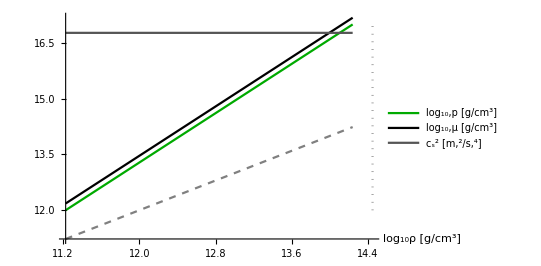

```mathematica
ParametricPlot[{{Log10[ρnuc],Log10[p]},{Log10[ρ[p]],Log10[ρ[p]]},{Log10[ρ[p]],Log10[p]},{Log10[ρ[p]],Log10[μ[p]]},{Log10[ρ[p]],Log10[10^-4 cs2[p] c^2]}},{p,10^12,10^17},PlotRange->All,AxesLabel->{"log_10ρ [g/cm^3]",None},AspectRatio->2/3,PlotLegends->Placed[{None,None,"log_10,p [g/cm^3]","log_10,μ [g/cm^3]","c_s^2 [m,^2/s,^4]"},After],PlotStyle->{Directive[Gray,Dotted],Directive[Gray,Dashed],Darker[Green],Black,Darker[Gray]}]
```

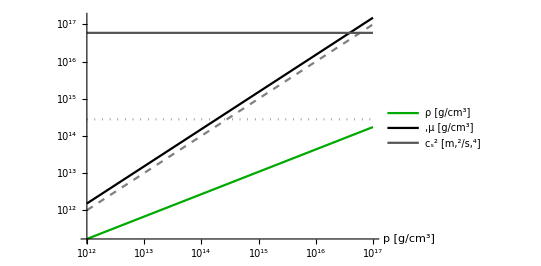

```mathematica
LogLogPlot[{ρnuc,p,ρ[p],μ[p],10^-4 cs2[p] c^2},{p,10^12,10^17},PlotRange->All,AxesLabel->{"p [g/cm^3]",None},AspectRatio->2/3,PlotLegends->Placed[{None,None,"ρ [g/cm^3]",",μ [g/cm^3]","c_s^2 [m,^2/s,^4]"},After],PlotStyle->{Directive[Gray,Dotted],Directive[Gray,Dashed],Darker[Green],Black,Darker[Gray]}]
```